```mathematica
x1=10;
x2=20;
d1=5;
d2=1.5;
posRules={0->{0,0},1->{x1,2*d1},2->{x1,d1},3->{x1,0},4->{x1,-d1},5->{x1,-2*d1},6->{x2,2*d1+d2},7->{x2,2*d1},8->{x2,2*d1-d2},9->{x2,d1+d2},10->{x2,d1},11->{x2,d1-d2},12->{x2,d2},13->{x2,0},14->{x2,-d2},15->{x2,-d1+d2},16->{x2,-d1},17->{x2,-d1-d2},18->{x2,-2*d1+d2},19->{x2,-2*d1},20->{x2,-2*d1-d2}};
```

```mathematica
pairs=Map[StringJoin@@#&,Tuples[{{"bologna, ","ham, ","cheese, ","chicken, ","beef, "},{"milk","coffee","tea"}}]];
```

```mathematica
vLabels=Map[(#+5->Placed[pairs[[#]],{15,0}])&,Range[15]]
```

{6→Placed[bologna, milk,{15,0}],7→Placed[bologna, coffee,{15,0}],8→Placed[bologna, tea,{15,0}],9→Placed[ham, milk,{15,0}],10→Placed[ham, coffee,{15,0}],11→Placed[ham, tea,{15,0}],12→Placed[cheese, milk,{15,0}],13→Placed[cheese, coffee,{15,0}],14→Placed[cheese, tea,{15,0}],15→Placed[chicken, milk,{15,0}],16→Placed[chicken, coffee,{15,0}],17→Placed[chicken, tea,{15,0}],18→Placed[beef, milk,{15,0}],19→Placed[beef, coffee,{15,0}],20→Placed[beef, tea,{15,0}]}

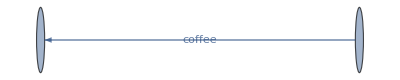

```mathematica
Graph[{Labeled[a->b,"coffee"]}]
```

```mathematica
Graph[{Labeled[0 -> 1,"bologna"],Labeled[0 -> 2,"ham"],Labeled[0 -> 3,"cheese"],Labeled[0 -> 4,"chicken"],Labeled[0 -> 5,"beef"],Labeled[1 -> 6,"milk"],Labeled[1 -> 7,"coffee"],Labeled[1 -> 8,"tea"],Labeled[2 -> 9,"milk"],Labeled[2 -> 10,"coffee"],Labeled[2 -> 11,"tea"],Labeled[3 -> 12,"milk"],Labeled[3 -> 13,"coffee"],Labeled[3 -> 14,"tea"],Labeled[4 -> 15,"milk"],Labeled[4 -> 16,"coffee"],Labeled[4 -> 17,"tea"],Labeled[5 -> 18,"milk"],Labeled[5 -> 19,"coffee"],Labeled[5 -> 20,"tea"]},VertexCoordinates->posRules,VertexLabels->Prepend[vLabels,0->Placed["Start",Above]],EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->.03}]]//Export["lunch.png",#,"PNG"]&
```

lunch.png

```mathematica
Directory[]
```

/Users/ken_l